# LyST - Field Equations

As equações de campo obtidas para a gravitação escalar-tensorial na variedade de Lyra são:

R_μν-1/2 g_μν R+2ϕ∇_μ ∇_ν ϕ-2ϕ g_μν∇_λ ∇^λ ϕ +3 g_μν∇_λ ϕ∇^λ ϕ  =,χϕ^2 T_μν.

O traço dessas equações pode ser útil em determinadas ocasiões. Calculando-o, encontra-se:

12∇_λ ϕ∇^λ ϕ -6ϕ ∇_λ ∇^λ ϕ-R  =,χ ϕ^2 T.

Deseja-se resolver as equações de campo impondo-se que o espaço-tempo respeita a simetria esférica. Essa consideração implica em se assumir um métrica da forma:

g_μν = (g_00(t,r) | g_01(t,r) | 0 | 0
g_01(t,r) | g_11(t,r) | 0 | 0
0 | 0 | g_22(t,r) | 0
0 | 0 | 0 | g_22(t,r)sin^2 θ)

Deseja-se resNesse trabalho, assume-se: 1) métrica estacionária e; 2) um sistema de coordenadas em que o tensor g_μν  possa ser escrita como:

g_μν = (α(r) | 0 | 0 | 0
0 | -β^-1(r) | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 sin^2 θ)

### Geometry

```mathematica
FileNameJoin[{$HOME=NotebookDirectory[],"_source"}]//SetDirectory;
Needs["sciPackage`"];Needs["LyST`"];
$HOME//SetDirectory;

MakeAssumption[{t∈Reals,r∈Reals,θ∈Reals,φ∈Reals,r>0,0≤θ<π,0≤φ<2π,α[r]≥0,ϕ[r] ≥ 0}];

CoordList = {t,r,θ,φ};

DefineScaleFunction[1];
DefineCoordinates[CoordList];
DefineMetric[DiagonalMatrix[{α[r],-α[r]^-1,-r^2,-r^2 Sin[θ]^2}]]
DefineChristoffel[]
DefineConnection[]
DefineCurvature[]
```

sciPackage, v.0.01-alpha - Scientific Package Tools.

This package is under construction. Be carefull.

LyST, v.00 .

This package is under construction. Be carefull.

### Covariant Derivatives of Scale

```mathematica
Unprotect[NablaPhiCov,NablaPhiCon];
ClearAll[NablaPhiCov,NablaPhiCon];

NablaPhiCov=Table[1/Φ D[Φ,𝕏[[1+𝒶]]],{𝒶,0,3}];
Notation[∇_i_ ϕ ⟺ NablaPhiCov[[i_+1]]];

NablaPhiCon=Table[1/Φ∑_(ℓ=0)^3 MetricCon[𝒶,ℓ]D[Φ,𝕏[[1+ℓ]]],{𝒶,0,3}];
Notation[∇^i_ ϕ ⟺ NablaPhiCon[[i_+1]]];

NablaNablaPhiCovCov=Table[Expand[1/Φ∂_𝒶 [∇_𝒷 ϕ]-∑_(ℓ=0)^3 (Subscript[Γ, {{𝒷, 𝒶}}]^ℓ∇_ℓ ϕ)],{𝒶,0,n},{𝒷,0,3}];
Notation[∇_i_ ∇_j_ ϕ ⟺ NablaNablaPhiCovCov[[i_+1,j_+1]]];

NablaNablaPhiCovCon=Table[Expand[1/Φ∂_𝒶 [∇^𝒷 ϕ]+∑_(ℓ=0)^3 (Subscript[Γ, {{ℓ, 𝒶}}]^𝒷∇^ℓ ϕ)],{𝒶,0,3},{𝒷,0,3}];
Notation[∇_i_ ∇^j_ ϕ ⟺ NablaNablaPhiCovCon[[i_+1,j_+1]]];

Protect[NablaPhiCov,NablaPhiCon];
```

### Checking Bianchi Identities

Contracting Curvature with Metric

```mathematica
CurvatureTensor[u,u,d,d] = Monitor[Table[
Expand[Sum[MetricCon[𝓈,𝓃]CurvatureTensor[𝓂,𝓈,𝒶,𝒷],{𝓈,0,n}]]
,{𝓂,0,3},{𝓃,0,3},{𝒶,0,3},{𝒷,0,3}],Grid[{{" Curvature Subscript[K, μναβ] "},{"μ: ",𝓂},{"ν: ",𝓃},{"α: ",𝒶},{"β: ",𝒷}}]];
Notation[Subscript[R, {{, , 𝓂_, 𝒶_}}]^{{𝓈_, 𝓃_}} ⟺ CurvatureTensor[u,u,d,d] [[1+𝓈_,1+𝓃_,1+𝓂_,1+𝒶_]]];

EinsteinMixM = Monitor[Table[
Expand[Sum[MetricCon[𝓈,𝒶]EinsteinCov[𝓈,𝒷],{𝓈,0,n}]]
,{𝒶,0,3},{𝒷,0,3}],Grid[{{" Einstein Mixed Tensor"},{"α: ",𝒶},{"β: ",𝒷}}]];
Notation[Subscript[G, {{, 𝒸_}}]^𝒷_ ⟺ EinsteinMixM[[1+𝒷_,1+𝒸_]]];
```

Calculating Covariant Derivative of Curvature

```mathematica
NablaCurv[u,u,d,d]=CovD[CurvatureTensor[u,u,d,d],{u,u,d,d}];
NablaCurv[u,d,d,d]=CovD[CurvatureTensorM,{u,d,d,d}];
NablaCurv[d,d,d,d]=CovD[CurvatureTensorCovM,{d,d,d,d}];
NablaRicci[d,d]=CovD[RicciCovM,{d,d}];
NablaRicci[u,d]=CovD[RicciMixM,{u,d}];
NablaEinstein[d,d]=CovD[EinsteinCovM,{d,d}];
NablaEinstein[u,d]=CovD[EinsteinMixM,{u,d}];

Notation[∇_𝒷_ Subscript[R, {{, , 𝓂_, 𝒶_}}]^{{𝓈_, 𝓃_}} ⟺ NablaCurv[u,u,d,d][[1+𝒷_,1+𝓈_,1+𝓃_,1+𝓂_,1+𝒶_]]];
Notation[∇_𝒷_ Subscript[R, {{, 𝓃_, 𝓂_, 𝒶_}}]^𝓈_ ⟺ NablaCurv[u,d,d,d][[1+𝒷_,1+𝓈_,1+𝓃_,1+𝓂_,1+𝒶_]]];
Notation[∇_𝒷_ Subscript[R, {{𝓈_, 𝓃_, 𝓂_, 𝒶_}}] ⟺ NablaCurv[d,d,d,d][[1+𝒷_,1+𝓈_,1+𝓃_,1+𝓂_,1+𝒶_]]];
Notation[∇_𝒶_ Subscript[R, {{𝒷_, 𝒸_}}] ⟺ NablaRicci[d,d][[1+𝒶_,1+𝒷_,1+𝒸_]]];
Notation[∇_𝒶_ Subscript[G, {{𝒷_, 𝒸_}}] ⟺ NablaEinstein[d,d][[1+𝒶_,1+𝒷_,1+𝒸_]]];
Notation[∇_𝒶_ Subscript[R, {{, 𝒸_}}]^𝒷_ ⟺ NablaRicci[u,d][[1+𝒶_,1+𝒷_,1+𝒸_]]];
Notation[∇_𝒶_ Subscript[G, {{, 𝒸_}}]^𝒷_ ⟺ NablaEinstein[u,d][[1+𝒶_,1+𝒷_,1+𝒸_]]];
Notation[∇_𝒶_ R ⟺ 1/Φ∂_𝒶_ [R]];
```

First Bianchi Identity

```mathematica
And[Evaluate[Sequence@@Flatten[Table[(Subscript[R, {{, 𝒷, 𝒸, 𝒹}}]^𝒶+Subscript[R, {{, 𝒸, 𝒹, 𝒷}}]^𝒶+Subscript[R, {{, 𝒹, 𝒷, 𝒸}}]^𝒶)===0,{𝒶,0,n},{𝒷,0,n},{𝒸,0,n},{𝒹,0,n}]]]]
```

True

Second Bianchi Identity

```mathematica
And[Evaluate[Sequence@@Flatten[Table[(∇_ℯ Subscript[R, {{, 𝒷, 𝒸, 𝒹}}]^𝒶+∇_𝒸 Subscript[R, {{, 𝒷, 𝒹, ℯ}}]^𝒶+∇_𝒹 Subscript[R, {{, 𝒷, ℯ, 𝒸}}]^𝒶)===0,{𝒶,0,n},{𝒷,0,n},{𝒸,0,n},{𝒹,0,n},{ℯ,0,n}]]]]
And[Evaluate[Sequence@@Flatten[Table[(∇_ℯ Subscript[R, {{, 𝒷, 𝒸, 𝒹}}]^𝒶 + ∇_𝒸 Subscript[R, {{, 𝒷, 𝒹, ℯ}}]^𝒶 + ∇_𝒹 Subscript[R, {{, 𝒷, ℯ, 𝒸}}]^𝒶)===0,{𝒶,0,n},{𝒷,0,n},{𝒸,0,n},{𝒹,0,n},{ℯ,0,n}]]]]
And[Evaluate[Sequence@@Flatten[Table[(∇_ℯ Subscript[R, {{, , 𝒸, 𝒹}}]^{{𝒶, 𝒷}} + ∇_𝒸 Subscript[R, {{, , 𝒹, ℯ}}]^{{𝒶, 𝒷}} + ∇_𝒹 Subscript[R, {{, , ℯ, 𝒸}}]^{{𝒶, 𝒷}})===0,{𝒶,0,n},{𝒷,0,n},{𝒸,0,n},{𝒹,0,n},{ℯ,0,n}]]]]

(* Contract Form *)
And[Evaluate[Sequence@@Flatten[Table[(∇_ℯ Subscript[R, {{, , 𝒸, 𝒹}}]^{{𝒶, 𝒷}} + ∇_𝒸 Subscript[R, {{, , 𝒹, ℯ}}]^{{𝒶, 𝒷}} - ∇_𝒹 Subscript[R, {{, , 𝒸, ℯ}}]^{{𝒶, 𝒷}})===0,{𝒶,0,n},{𝒷,0,n},{𝒸,0,n},{𝒹,0,n},{ℯ,0,n}]]]]
And[Evaluate[Sequence@@Flatten[Table[∑_(𝒶=0)^n (∇_𝒶 Subscript[R, {{, , 𝒸, 𝒹}}]^{{𝒶, 𝒷}} + ∇_𝒸 Subscript[R, {{, , 𝒹, 𝒶}}]^{{𝒶, 𝒷}} - ∇_𝒹 Subscript[R, {{, , 𝒸, 𝒶}}]^{{𝒶, 𝒷}})===0,{𝒷,0,n},{𝒸,0,n},{𝒹,0,n}]]]]
And[Evaluate[Sequence@@Flatten[Table[FullSimplify[∑_(𝒶=0)^n (∇_𝒶 Subscript[R, {{, , 𝒹, 𝒸}}]^{{𝒷, 𝒶}}  )+∇_𝒸 Subscript[R, {{, 𝒹}}]^𝒷-∇_𝒹 Subscript[R, {{, 𝒸}}]^𝒷 ]===0,{𝒷,0,n},{𝒸,0,n},{𝒹,0,n}]]]]
And[Evaluate[Sequence@@Flatten[Table[FullSimplify[∑_(𝒶=0)^n ∑_(𝒷=0)^n (∇_𝒶 Subscript[R, {{, , 𝒹, 𝒷}}]^{{𝒷, 𝒶}}  )+∑_(𝒷=0)^n ∇_𝒷 Subscript[R, {{, 𝒹}}]^𝒷-∑_(𝒷=0)^n ∇_𝒹 Subscript[R, {{, 𝒷}}]^𝒷 ]===0,{𝒹,0,n}]]]]
And[Evaluate[Sequence@@Flatten[Table[Expand[FullSimplify[2∑_(𝒷=0)^n ∇_𝒷 Subscript[R, {{, 𝒹}}]^𝒷-∇_𝒹 R ]]===0,{𝒹,0,n}]]]]
And[Evaluate[Sequence@@Flatten[Table[Expand[FullSimplify[2∑_(𝒷=0)^n ∇_𝒷 Subscript[G, {{, 𝒹}}]^𝒷]]===0,{𝒹,0,n}]]]]
```

True

True

True

«6 more identical outputs»

```mathematica
Table[∑_(𝒶=0)^n (∇_𝒶 Subscript[R, {{, , 𝒹, 𝒸}}]^{{𝒷, 𝒶}}  )+∇_𝒸 Subscript[R, {{, 𝒹}}]^𝒷-∇_𝒹 Subscript[R, {{, 𝒸}}]^𝒷 ===0,{𝒷,0,n},{𝒸,0,n},{𝒹,0,n}][[3,2,3]]
```

False

```mathematica
Block[{𝒷=3,𝒸=2,𝒹=3},FullSimplify[
∑_(𝒶=0)^n (∇_𝒶 Subscript[R, {{, , 𝒹, 𝒸}}]^{{𝒷, 𝒶}}  )+∇_𝒸 Subscript[R, {{, 𝒹}}]^𝒷-∇_𝒹 Subscript[R, {{, 𝒸}}]^𝒷 ]
]
```

0

```mathematica
CurvatureFormulaM=Table[Expand[
(1/Φ^2 Subscript[ℛ, {{, ℓ, 𝒶, 𝒷}}]^𝓂+1/Φ(Subscript[δ, 𝒷]^𝓂∇_𝒶 ∇_ℓ ϕ-Subscript[δ, 𝒶]^𝓂∇_𝒷 ∇_ℓ ϕ+Subscript[g, {{ℓ, 𝒶}}]∇_𝒷 ∇^𝓂 ϕ-Subscript[g, {{ℓ, 𝒷}}]∇_𝒶 ∇^𝓂 ϕ)+
+1/Φ^2(Subscript[g, {{ℓ, 𝒷}}] Subscript[δ, 𝒶]^𝓂-Subscript[g, {{ℓ, 𝒶}}] Subscript[δ, 𝒷]^𝓂)∑_(𝓇=0)^n ∇_𝓇 ϕ∇^𝓇 ϕ)]
,{𝓂,0,3},{ℓ,0,3},{𝒶,0,3},{𝒷,0,3}];
CurvatureTensorM===CurvatureFormulaM
```

True

### Stress-Energy Tensor

```mathematica
StressEnergyTensorM//ClearAll
StressEnergyTensorM[u,d]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});

Notation[Subscript[T, 𝒷_]^𝒶_  ⟺  StressEnergyTensorM[u,d][[𝒶_+1,𝒷_+1]]];

StressEnergyTensorM[d,d]=Table[∑_(ℓ=0)^n g^{{𝒶, ℓ}}Subscript[T, ℓ]^𝒷,{𝒶,0,n},{𝒷,0,n}];
Notation[Subscript[T, {{𝒶_, 𝒷_}}] ⟺ StressEnergyTensorM[d,d][[𝒶_+1,𝒷_+1]]];

NablaStressEnergy[u,d]=CovD[StressEnergyTensorM[u,d],{u,d}];
Notation[∇_𝒶_ Subscript[T, {{, 𝒸_}}]^𝒷_ ⟺ NablaStressEnergy[u,d][[1+𝒶_,1+𝒷_,1+𝒸_]]];
```

```mathematica
StressEnergyTensorM[d,d]
```

```mathematica
StressEnergyTensorM[d,d]
```

{{ρ[t],0,0,0},{0,p[t],0,0},{0,0,p[t],0},{0,0,0,p[t]}}

### Covariant Derivative of Scale Function

```mathematica
DelPhi[d] =Table[∂_𝒶 [Φ],{𝒶,0,n}];
Notation[∂_i_ ϕ ⟺ DelPhi[d][[i_+1]]];

NablaPhi[d]=Table[1/Φ∂_𝒶 [Φ],{𝒶,0,n}];
Notation[∇_i_ ϕ ⟺ NablaPhi[d][[i_+1]]];

NablaPhi[u]=Table[1/Φ∑_(ℓ=0)^n g^{{𝒶, ℓ}}∂_ℓ [Φ],{𝒶,0,n}];
Notation[∇^i_ ϕ ⟺ NablaPhi[u][[i_+1]]];

NablaNablaPhi[d,d]=Table[Expand[1/Φ∂_𝒶 [∇_𝒷 ϕ]-∑_(ℓ=0)^n (Subscript[Γ, {{𝒷, 𝒶}}]^ℓ∇_ℓ ϕ)],{𝒶,0,n},{𝒷,0,n}];
Notation[∇_i_ ∇_j_ ϕ ⟺ NablaNablaPhi[d,d][[i_+1,j_+1]]];

NablaNablaPhi[d,u]=Table[Expand[1/Φ∂_𝒶 [∇^𝒷 ϕ]+∑_(ℓ=0)^n (Subscript[Γ, {{ℓ, 𝒶}}]^𝒷∇^ℓ ϕ)],{𝒶,0,n},{𝒷,0,n}];
Notation[∇_i_ ∇^j_ ϕ ⟺ NablaNablaPhi[d,u][[i_+1,j_+1]]];
```

## Action Integrand

The action for LyST gravity is a Lyra generalization of Einstein-Hilbert Action:

S = ∫d^4 x √-g ϕ^4 R

where  d^4 x √-g ϕ^4   is the Lyra invariant hipervolume element and R the Lyra scalar of curvature. To obtain the field equations, let's consider the lagrangian:

L= √-g ϕ^4 R

and use a Euler-Lagrange equation for each undefined function of the system. (In spherically symmetric case, are α(r) and ϕ(r) )

```mathematica
L = FullSimplify[√-g Φ^4 R]/.{θ->π/2};
Print["Lagrangian:\n\t L =√-gΦ^4R = ",Expand[L]]
Eq[α] = FullSimplify[Expand[D[L,α[r]]-D[D[L,α'[r]],r]+D[D[L,α''[r]],{r,2}]]];
Print["Field Equation for α:\n\t  ",Eq[α]," = 0"]

Eq[ϕ] = FullSimplify[Expand[D[L,ϕ[r]]-D[D[L,ϕ'[r]],r]+D[D[L,ϕ''[r]],{r,2}]]];
Print["Field Equation for ϕ:\n\t  ",Expand[Eq[ϕ]]," = 0"]
```

Lagrangian:
	 L =√-gΦ^4R = 2-2 α[r]-4 r α'[r]-r^2 α''[r]

Field Equation for α:
	  0 = 0

Field Equation for ϕ:
	  0 = 0

A specific solution for this system is:

α = (1-r/r_L)^2(1-(2m)/r+(2m)/r_L) ,
	ϕ =(1-r/r_L)^-1.

Here, it's convenient to check if it really is a solution of the field equations:

```mathematica
SphSymmSol = {
	α -> Function[r,(1-r/rL)^2(1-(2m)/r+(2m)/rL)],
	ϕ -> Function[r,(1-r/rL)^-1]
};

Print["It's ok if both values are zero: ",{
	FullSimplify[Expand[Eq[α]/.SphSymmSol]],
	FullSimplify[Expand[Eq[ϕ]/.SphSymmSol]]
}]
```

It's ok if both values are zero: {0,0}

This solution is special because the General Relativity can be recovered as limit of  r_L→∞. 

However, that's not the most general solution. Let's find out which one would be. Solving field equations  algebraically

```mathematica
Solϕ = DSolve[Eq[α]==0,ϕ,r][[1]];
Solα = DSolve[Expand[Eq[ϕ]/.Solϕ]==0,α,r][[1]];
eϕ = FullSimplify[ϕ[r]/.Solϕ];
eα = FullSimplify[α[r]/.Solα];
Print["Solution for ϕ:\n\t\tϕ(r)=",eϕ]
Print["\nSolution for α:\n\t\tα(r)=",eα]
```

Solution for ϕ:
		ϕ(r)=C[2]/(r+C[1])

Solution for α:
		α(r)=((r+C[1])^2 (1+(r+C[1]) (C[3]+r C[4])))/r^2

## Variational Principle on Action

## Field Equations

Left member of the Einstein`s Equations

```mathematica
Unprotect[α,rL];
ClearAll[α,rL];
ClearAll[α,β,ϕ,H];
(*RedefineFormat[{α,β,ϕ}];*)

(*EqEinsteinL[𝓂_,𝓃_]:=Expand[FullSimplify[
1/Φ^2(Subscript[ℛ, {{𝓂, 𝓃}}]-1/2 Subscript[g, {{𝓂, 𝓃}}] ℛ)+ 2 1/Φ∇_𝓂 ∇_𝓃 ϕ - 2/Φ Subscript[g, {{𝓂, 𝓃}}]∑_(ℓ=0)^n ∇_ℓ ∇^ℓ ϕ + 3/Φ^2 Subscript[g, {{𝓂, 𝓃}}]∑_(ℓ=0)^n ∇_ℓ ϕ∇^ℓ ϕ
]];*)

EqEinsteinL[𝓂_,𝓃_]:=Expand[FullSimplify[(Subscript[R, {{𝓂, 𝓃}}]-1/2 Subscript[g, {{𝓂, 𝓃}}] R)]];

Subs={};

EQL[0]=Expand[((EqEinsteinL[0,0]+κ Subscript[T, {{0, 0}}]))/.Subs/.Subs];
EQL[1]=Expand[( EqEinsteinL[1,1]+κ Subscript[T, {{1, 1}}])/.Subs/.Subs];
EQL[2]=Expand[( EqEinsteinL[2,2]+κ Subscript[T, {{2, 2}}])/.Subs/.Subs];



(* Conservation *)
EQL[3]=(∑_(ℓ=0)^n ∇_ℓ Subscript[T, {{, 0}}]^ℓ)/.{a->Function[t,a[t]]}/.Subs;

Do[Print[(EQL[i]==0)//TraditionalForm],{i,0,2}];

EQL[4] = Expand[FullSimplify[ℛ +6 Φ ∑_(ℓ=0)^n ∇_ℓ ∇^ℓ ϕ -12∑_(ℓ=0)^n ∇_ℓ ϕ∇^ℓ ϕ]];
```

(α(r))^2/r^2-(α(r))/r^2+(α(r) α'(r))/r==0

1/(r^2 α(r))-1/r^2-(α'(r))/(r α(r))==0

-1/2 r^2 α''(r)-r α'(r)==0

First Einstein Equation

```mathematica
(Expand[Φ^2/(r^2 α[r]) EQL[2]]/.{ϕ''[r]->ϕ'',ϕ'[r]->ϕ',ϕ[r]->ϕ,α''[r]->α'',α'[r]->α',α[r]->α})//TraditionalForm//TeXForm
```

-\frac{\alpha ''}{2 \alpha }-\frac{\alpha '}{\alpha  r}

### Checking Solution

α(r) = (1-r/r_L)^2(1-(2m)/r+(2m)/r_L)           e           ϕ(r) = (1-r/r_L)^-1

```mathematica
Unprotect[α,rL];
ClearAll[α,rL];
α[r_]:=(1-(2m)/r);
ϕ[r_]:=1;
Protect[α,rL];

Table[EQL[i]//FullSimplify,{i,0,3}]
FullSimplify[(α'[r] ϕ'[r])/(α[r] ϕ[r])-1/(α[r] r^2)+1/r^2+α'[r]/(r α[r])+4 ϕ'[r]/(r ϕ[r])+2 ϕ''[r]/ϕ[r]-ϕ'[r]^2/ϕ[r]^2]
FullSimplify[-(α'[r] ϕ'[r])/(α[r] ϕ[r])+1/(α[r] r^2)-1/r^2-α'[r]/(r α[r])-4 ϕ'[r]/(r ϕ[r])-3 ϕ'[r]^2/ϕ[r]^2]
FullSimplify[-α'[r]/(r α[r])-2 ϕ'[r]/(r ϕ[r])-α''[r]/(2α[r])-2(α'[r]ϕ'[r])/(α[r]ϕ[r])-2 ϕ''[r]/ϕ[r]+ϕ'[r]^2/ϕ[r]^2]
```

{0,0,0,0}

0

0

0

```mathematica
Unprotect[α,rL];
ClearAll[α,rL];
(*α[r_]:=(1-r/rL)^2(1-(2m)/r+(2m)/rL);*)
(*α[r_]:=C[1]/r(1+r/C[1])^2(C[3]+C[3]/C[1] r-1);*)
(*α[r_]:=((C[1]+r)^2(r+C[1]-C[1]/C[3]))/r C[3]/C[1]^2;*)
α[r_]:=(1-rs/r);

ϕ[r_]:=1;
Protect[α,rL];

Table[EQL[i]//FullSimplify,{i,0,3}]
```

{0,0,0,0}

### Einstein Equations

```mathematica
Unprotect[α,ϕ,rL];
ClearAll[α,ϕ,rL];

EqForm[expr_]:=TeXForm[TraditionalForm[
expr/.{
α[r] -> α , α'[r] -> α' , α''[r] -> α'',
ϕ[r] -> ϕ , ϕ'[r] -> ϕ' , ϕ''[r] -> ϕ'',
z[r] -> z , z'[r] -> z
}
]]
```

```mathematica
EQ[0]=Expand[1/α[r]^2 FullSimplify[EQL[0]]]
EQ[1]=Expand[FullSimplify[EQL[1]]]
EQ[2]=Expand[1/(r^2 α[r])FullSimplify[EQL[2]]]
```

1/r^2-1/(r^2 α[r])+α'[r]/(r α[r])

-1/r^2+1/(r^2 α[r])-α'[r]/(r α[r])

-α'[r]/(r α[r])-α''[r]/(2 α[r])

```mathematica
DSolve[-α'[r]/(r α[r])-α''[r]/(2 α[r])==0,α,r]
```

{{α→Function[{r},-C[1]/r+C[2]]}}

Somando as duas primeiras equações e dividindo o resultado por 2:

```mathematica
EQ[3] = Expand[(EQ[0]+EQ[1])/2]

EQ[3]/.{ϕ->Function[r,A/(b-r)]}
```

0

0

```mathematica
Solve[(C[1]+r)^2(r C[3]+C[3]C[1]-C[1])/(r C[1]^2)==0,r]
```

{{r→-C[1]},{r→-C[1]},{r→(C[1]-C[1] C[3])/C[3]}}

Definindo um nova variável  z = ϕ'/ϕ  tal que   z'=-z^2+ϕ''/ϕ, logo:

```mathematica
SubsZ = {ϕ'[r]->z[r]ϕ[r],ϕ''[r]->ϕ[r](z'[r]+z[r]^2)}
EQ[3]/.SubsZ
```

{ϕ'[r]→z[r] ϕ[r],ϕ''[r]→ϕ[r] (z[r]^2+z'[r])}

-z[r]^2+z'[r]

Dessa forma, EQ[3] pode ser reescria como:

```mathematica
EQz[3]=EQ[3]/.SubsZ
```

-z[r]^2+z'[r]

Reescrevendo EQ[1] em termos de z;

```mathematica
EQz[1] = EQ[1]/.SubsZ

(*EqForm[EQz[1]]*)
```

-1/r^2-(4 z[r])/r-3 z[r]^2+1/(r^2 α[r])-α'[r]/(r α[r])-(z[r] α'[r])/α[r]

Resolvendo para z

```mathematica
SolZ = DSolve[EQz[3]==0,z,r][[1]]
```

{z→Function[{r},1/(-r-C[1])]}

```mathematica
Collect[Expand[FullSimplify[
(-1/(r α[r])-1/((-r-C[1]) α[r]))^-1 C[1](EQz[1]/.SolZ)]],{α'[r],α[r]}]
```

-1-C[1]/r+(-(2 C[1])/(r+C[1])+C[1]^2/(r (r+C[1]))) α[r]+C[1] α'[r]

```mathematica
expr = C[1] α'[r]+((1-(2r)/C[1])/(1+r/C[1])) (C[1]α[r])/r-1-C[1]/r

Expand[FullSimplify[expr]]==
Expand[FullSimplify[Collect[Expand[FullSimplify[
(-1/(r α[r])-1/((-r-C[1]) α[r]))^-1 C[1](EQz[1]/.SolZ)]],{α'[r],α[r]}]
]]
```

-1-C[1]/r+((1-(2 r)/C[1]) C[1] α[r])/(r (1+r/C[1]))+C[1] α'[r]

True

```mathematica
C[1] α'[r] +α[r] C[1]/r((1-(2r)/C[1])/(1+r/C[1]))  == 1+C[1]/r
```

((1-(2 r)/C[1]) C[1] α[r])/(r (1+r/C[1]))+C[1] α'[r]==1+C[1]/r

```mathematica
rL α'[r] +α[r] rL/r((1+(2r)/rL)/(1-r/rL))  +(1-rL/r) == 0
```

1-rL/r+((1+(2 r)/rL) rL α[r])/(r (1-r/rL))+rL α'[r]==0

```mathematica
(* Equacao antes de (19) do Artigo 1 *)
DSolve[C[1] α'[r] +α[r] C[1]/r((1-(2r)/C[1])/(1+r/C[1]))  == 1+C[1]/r,α,r]
```

{{α→Function[{r},-(r+C[1])^2/(r C[1])+((r+C[1])^3 C[2])/r]}}

```mathematica
DSolve[ α'[r] +α[r] 1/r((1-(2r)/1)/(1+r/1))  == 1+1/r,α,r]
```

{{α→Function[{r},-(1+r)^2/r+((1+r)^3 C[1])/r]}}

```mathematica
DSolve[ α'[ρ] +α[ρ]/ρ((1-2ρ)/(1+ρ))  == 1+1/ρ,α,ρ]
```

{{α→Function[{ρ},-(1+ρ)^2/ρ+((1+ρ)^3 C[1])/ρ]}}

```mathematica
Unprotect[ϕ,α,rL];
ClearAll[ϕ,α,rL];

ϕ[r_]:=1/(1-r/rL);
expr = Collect[Expand[ α[r](r^2-r rL)FullSimplify[-(α'[r] ϕ'[r])/(α[r] ϕ[r])+1/(α[r] r^2)-1/r^2-α'[r]/(r α[r])-4 ϕ'[r]/(r ϕ[r])-3 ϕ'[r]^2/ϕ[r]^2]],{α'[r],α[r]}]
```

r^2/(r-rL)^2-(3 r rL)/(r-rL)^2+(3 rL^2)/(r-rL)^2-rL^3/(r (r-rL)^2)+(-(2 r rL)/(r-rL)^2+rL^2/(r-rL)^2+rL^3/(r (r-rL)^2)) α[r]+((r^2 rL)/(r-rL)^2-(2 r rL^2)/(r-rL)^2+rL^3/(r-rL)^2) α'[r]

```mathematica
FullSimplify[Coefficient[expr,α'[r]]]
FullSimplify[Coefficient[expr,α[r]]]
FullSimplify[r^2/(r-rL)^2-(3 r rL)/(r-rL)^2+(3 rL^2)/(r-rL)^2-rL^3/(r (r-rL)^2)]
```

rL

3+rL/r+(3 r)/(-r+rL)

1-rL/r

```mathematica
3+rL/r+(3 r)/(-r+rL)==rL/r(1 + 2 r/rL)/(1-r/rL)
```

```mathematica
(* Logo *)

1-rL/r+rL/r(1 + 2 r/rL)/(1-r/rL)α[r]+rL α'[r]==0
```

```mathematica
expr = α[ρ]/.DSolve[1-1/ρ+α[ρ]/ρ(1 + 2 ρ)/(1-ρ)+α'[ρ]==0,α,ρ][[1]]
```

-(1-ρ)^3/((-1+ρ) ρ)+((1-ρ)^3 C[1])/ρ

```mathematica
A = ((1-ρ)^2/ρ+((1-ρ)^3 C[1])/ρ)
```

(1-ρ)^2/ρ+((1-ρ)^3 C[1])/ρ

```mathematica
A = (1-ρ)^2/ρ+[1+(1-ρ) C[1]]
```

{{ρ→1},{ρ→1},{ρ→(1+C[1])/C[1]}}

```mathematica
ρs == 1+1/C[1]
```

{{C[1]→1/(-1+ρs)}}

### Novo Caso

```mathematica
Unprotect[α,rL];
ClearAll[α,rL];
α[r_]:=(1-r/rL)^2/(1-rs/rL)(1-rs/r);
α[r_]:=rL/r(1-r/rL)^2
Expand[FullSimplify[rL α'[r] +α[r] rL/r((1+(2r)/rL)/(1-r/rL))  +(1-rL/r)]]
(*α[r_]:=rL/r(1-r/rL)^2
ϕ[r_]:=1/(1-r/rL);*)
Protect[α,rL];
```

0

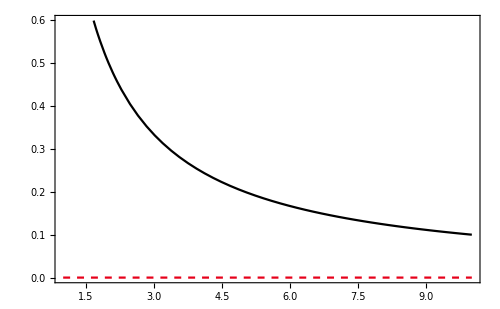

```mathematica
Plot[{1/(1-r)^2 1/r(1-r)^2,0},{r,1,10}]
```

```mathematica
Expand[rL/r(1-r/rL)^2]
```

-2+r/rL+rL/r

### Geodesics

Making the coordinates dependent on an affine parameter

```mathematica
param = λ;

ParameterizedCoordinates = Table[coord[param],{coord,𝕏}];

Notation[𝓍^i_ ⟺ ParameterizedCoordinates[[i_+1]]];

SubsParamCoord = Table[coord->coord[param],{coord,𝕏}];

SubsConditions = {θ->Function[{λ},π/2]};


EqGeo = Table[Block[{},
D[(x^𝓃)[λ],{λ,2}]+FullSimplify[∑_(𝒶=0)^n ∑_(𝒷=0)^n ((({{{𝓃}, {{{𝒶, 𝒷}}}}}+∇_𝒶 ϕ Subscript[δ, 𝒷]^𝓃+∇_𝒷 ϕ Subscript[δ, 𝒶]^𝓃-∑_(𝓂=0)^n ∇_𝓂 ϕ Subscript[g, {{𝒶, 𝒷}}] g^{{𝓂, 𝓃}})/.SubsParamCoord )D[(x^𝒶)[λ],{λ,2}]D[(x^𝒷)[λ],{λ,2}])/.SubsConditions]
],{𝓃,0,3}]
```

{t''[λ]-(((rL+r[λ]) ϕ[r[λ]]+2 r[λ] (-rL+r[λ]) ϕ'[r[λ]]) r''[λ] t''[λ])/((rL-r[λ]) r[λ] ϕ[r[λ]]),r''[λ]+1/(2 rL^2 (rL-r[λ])^2 r[λ]^3 ϕ[r[λ]])(rL^2 (rL-r[λ]) r[λ]^2 ((rL+r[λ]) ϕ[r[λ]]+2 (rL-r[λ]) r[λ] ϕ'[r[λ]]) r''[λ]^2+(rL-r[λ])^5 (-(rL+r[λ]) ϕ[r[λ]]+2 (rL-r[λ]) r[λ] ϕ'[r[λ]]) t''[λ]^2-2 rL (rL-r[λ])^4 r[λ]^3 (ϕ[r[λ]]+r[λ] ϕ'[r[λ]]) φ''[λ]^2),θ''[λ],φ''[λ]+2 (1/r[λ]+ϕ'[r[λ]]/ϕ[r[λ]]) r''[λ] φ''[λ]}

#### Equations

ϕ^2 α(r) ṫ = k

k^2/(α(r) ϕ^2(r))-(ϕ^2(r))/(α(r))(ṙ)^2 -h^2/(r^2 ϕ^2(r)) = 1

ϕ^2 r^2 φ̇ = h

#### Massive Radial Trajectory

ϕ^2 r^2 φ̇ = h=0

Hence:

ϕ^2 α(r) ṫ = k

(ṙ)^2=k^2/(ϕ^4(r))-α(r)ϕ^-2(r)